```mathematica
Q3coef[k_]:=-2/(Pi(1+4 k^2))(ⅇ^(-π/2)*(-1)^k-1)(1-2 I k)
```

```mathematica
Q3func[x_]=∑_(k=-30)^30 Q3coef[k]*ⅇ^(I 2 k x);
```

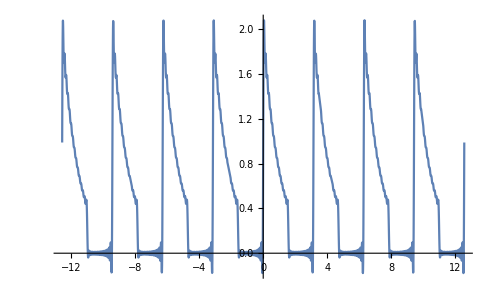

```mathematica
Plot[Q3func[x],{x,-4 Pi,4 Pi}]
```

```mathematica
Torr=1
T0=2*Torr
Q4coef[k_]:=1/(2π)((ⅇ^(-I k Pi Torr/T0)-ⅇ^(I k Pi Torr/T0))/(-I k))
```

1

2

```mathematica
Q4func[x_]:=∑_(k=-100)^-1 Q4coef[k]*ⅇ^(x I k 2 Pi/T0)+∑_(k=1)^100 Q4coef[k]*ⅇ^(x I k 2 Pi/T0)+Torr/T0
```

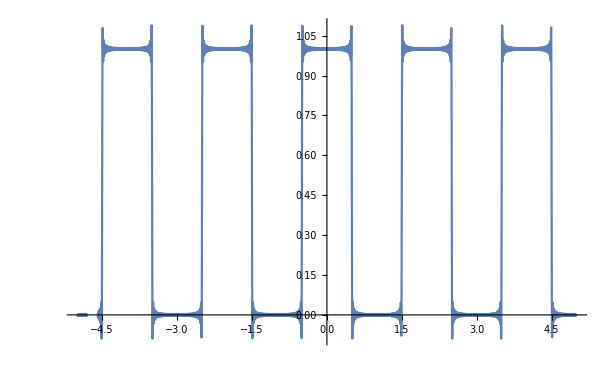

```mathematica
Plot[Q4func[x],{x,-5,5}]
```